# Вариант 13

```mathematica
f[x_]:=(x^6+4*x^2+1)^(1/5)*Sin[(2*x)/(√31)+1/7*√(x+5)+1/18];
```

### Задание 1 . n=6 a)

```mathematica
A=0; B=6; n=6; H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 0.366267
1. | 0.990682
2. | 2.20005
3. | 3.77226
4. | 4.97336
5. | 5.13549
6. | 3.79068

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];
```

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*∏_(j=1)^n If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1];
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=", Ln];
```

Ln(x)=0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6

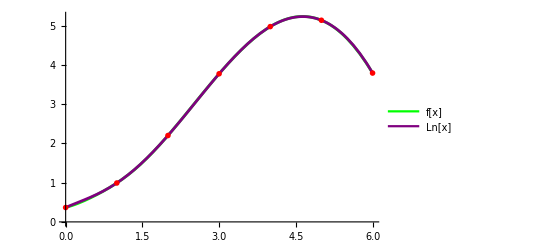

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.01],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Ln[x]"}]]
```

```mathematica
б)
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=0]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

0.366267 | 0.624416 | 0.584948 | -0.222101 | -0.511854 | 0.577936 | -0.444101
0.990682 | 1.20936 | 0.362847 | -0.733954 | 0.0660824 | 0.133835 | 0
2.20005 | 1.57221 | -0.371107 | -0.667872 | 0.199918 | 0 | 0
3.77226 | 1.2011 | -1.03898 | -0.467954 | 0 | 0 | 0
4.97336 | 0.162125 | -1.50693 | 0 | 0 | 0 | 0
5.13549 | -1.34481 | 0 | 0 | 0 | 0 | 0
3.79068 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
в)
```

```mathematica
NewtonInterpolationMultiplier[dataX_,n_,i_,H_]:=(∏_(k=1)^i ((x-dataX[[n]])/H+k-1))/(i!)
NewtonInterpolationSecondMethod[dataX_,dataY_,deltaTable_,H_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) (NewtonInterpolationMultiplier[dataX,n,i,H]*deltaTable[[n-i,i+1]]);
```

```mathematica
Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)="Pn];
```

Pn(x)= (0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6)

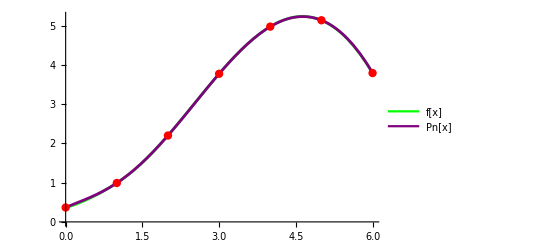

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Pn,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Pn[x]"}]]
```

```mathematica
г)
```

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6

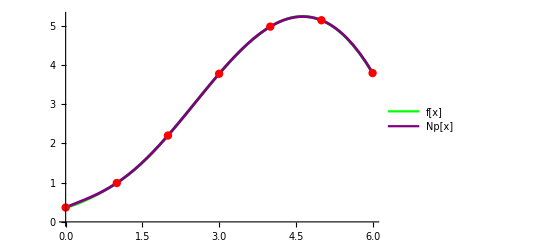

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Np,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Np[x]"}]]
```

```mathematica
д)
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Ln[2.4316]= ",Ln/.x->2.4316];
Print["Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 2.8766

Ln[2.4316]= 2.87389

Pn[2.4316]= 2.87389

Np[2.4316]= 2.87389

```mathematica
ж)
```

```mathematica
Rn=Abs[f[x]-Np];
```

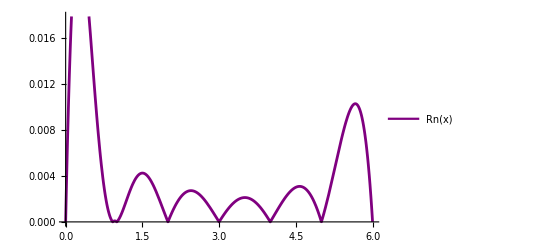

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Purple];
Legended[Show[func1],LineLegend[{Purple},{"Rn(x)"}]]
```

```mathematica
е)
```

```mathematica
FindMaximum[{Rn,A<=x<=B},x]
```

{0.0247999,{x→0.261447}}

### Задание 1 . n=10 a)

```mathematica
n=10; H=B/n; data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=",Ln];
```

Ln(x)=0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

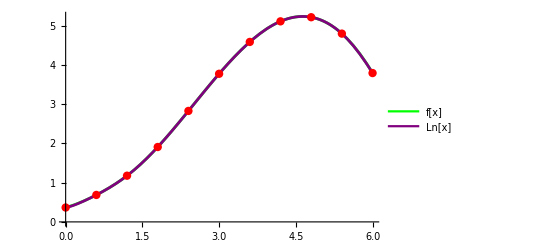

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Ln[x]"}]]
```

```mathematica
б)
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData, Frame->All]
```

0.366267 | 0.32024 | 0.169814 | 0.0707817 | -0.123247 | 0.0150689 | 0.0910209 | -0.183756 | 0.270722 | -0.349071 | 0.415615
0.686507 | 0.490054 | 0.240596 | -0.0524654 | -0.108178 | 0.10609 | -0.092735 | 0.0869664 | -0.0783483 | 0.0665447 | 0
1.17656 | 0.73065 | 0.18813 | -0.160644 | -0.00208834 | 0.0133549 | -0.00576856 | 0.00861809 | -0.0118037 | 0 | 0
1.90721 | 0.91878 | 0.0274868 | -0.162732 | 0.0112665 | 0.00758631 | 0.00284953 | -0.00318558 | 0 | 0 | 0
2.82599 | 0.946267 | -0.135245 | -0.151465 | 0.0188528 | 0.0104358 | -0.000336051 | 0 | 0 | 0 | 0
3.77226 | 0.811022 | -0.286711 | -0.132613 | 0.0292887 | 0.0100998 | 0 | 0 | 0 | 0 | 0
4.58328 | 0.524311 | -0.419323 | -0.103324 | 0.0393885 | 0 | 0 | 0 | 0 | 0 | 0
5.10759 | 0.104988 | -0.522647 | -0.0639355 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.21258 | -0.417659 | -0.586582 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.79492 | -1.00424 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.79068 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
в)
```

```mathematica
Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)=",Pn];
```

Pn(x)=0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

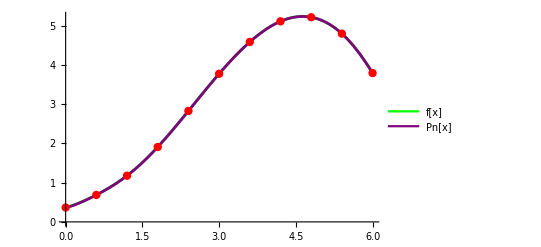

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Pn[x]"}]]
```

```mathematica
г)
```

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

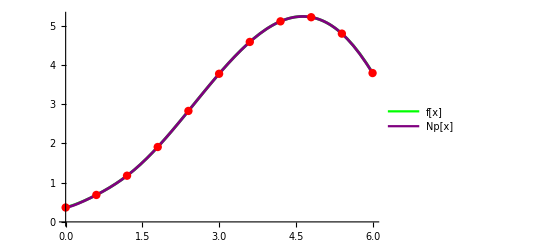

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Np[x]"}]]
```

```mathematica
д)
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print[ "Ln[2.4316]= ",Ln/.x->2.4316];
Print[ "Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 2.8766

Ln[2.4316]= 2.87663

Pn[2.4316]= 2.87663

Np[2.4316]= 2.87663

```mathematica
ж)
```

```mathematica
Rn=Abs[f[x]-Np];
```

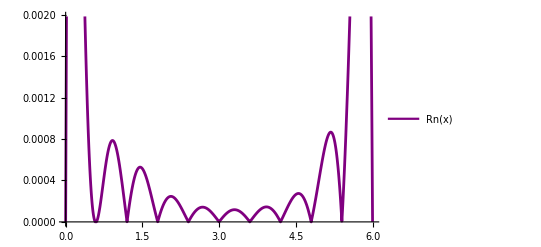

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Purple];
Legended[Show[func1],LineLegend[{Purple},{"Rn(x)"}]]
```

```mathematica
е)
```

```mathematica
FindMaximum[{Rn,A<=x<=B},{x,0}]
```

{0.0072881,{x→0.133415}}

### Задание 2 . n=6 a)

```mathematica
n=6;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i];]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.92478 | 3.94979
5.34549 | 4.85644
4.30165 | 5.15814
3. | 3.77226
1.69835 | 1.76629
0.654506 | 0.723811
0.0752163 | 0.395238

```mathematica
DividedDifferenceRecursive[dataX_,dataY_,begin_,end_]:=If[begin+1==end,(dataY[[end]]-dataY[[begin]])/(dataX[[end]]-dataX[[begin]]),(DividedDifferenceRecursive[dataX,dataY,begin+1,end]-DividedDifferenceRecursive[dataX,dataY,begin,end-1])/(dataX[[end]]-dataX[[begin]])]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,	For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

3.94979 | -1.56512 | -0.786191 | -0.0714674 | 0.00866198 | 0.00142088 | -0.000576143
4.85644 | -0.289025 | -0.577165 | -0.108077 | 0.00117354 | 0.00479107 | 0
5.15814 | 1.06471 | -0.182993 | -0.113582 | -0.0240767 | 0 | 0
3.77226 | 1.5411 | 0.231256 | -0.011823 | 0 | 0 | 0
1.76629 | 0.998688 | 0.265836 | 0 | 0 | 0 | 0
0.723811 | 0.567201 | 0 | 0 | 0 | 0 | 0
0.395238 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
б)
```

```mathematica
NewtonDivDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=0.352119+0.589375 x-0.243131 x^2+0.393646 x^3-0.11905 x^4+0.0134766 x^5-0.000576143 x^6

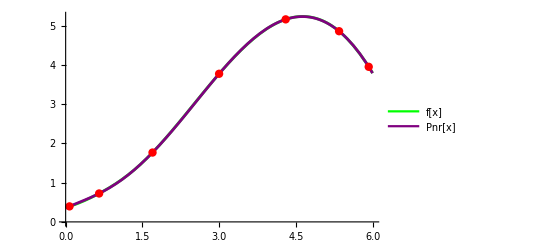

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Pnr[x]"}]]
```

```mathematica
в)
```

```mathematica
Intf = Interpolation[data];
```

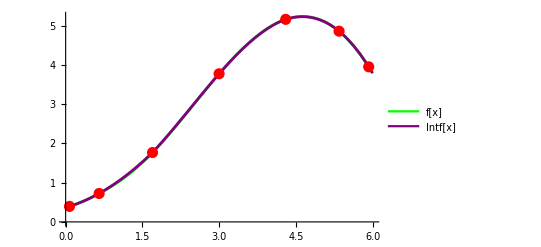

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Intf[x]"}]]
```

```mathematica
г)
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print[ "Pnr[2.4316]= ",Pnr/.x->2.4316];
Print["Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 2.8766

Pnr[2.4316]= 2.87181

Intf[2.4316]= 2.88404

```mathematica
д)
```

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},x]
```

{0.00518282,{x→0.919784}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],A<=x<=B},x]
```

{0.0238141,{x→1.25976}}

### Задание 2 . n=10 a)

```mathematica
n=10;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i]]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.96946 | 3.85642
5.7289 | 4.31931
5.26725 | 4.93631
4.62192 | 5.23197
3.8452 | 4.84025
3. | 3.77226
2.1548 | 2.43768
1.37808 | 1.36639
0.732751 | 0.77941
0.271104 | 0.487098
0.0305357 | 0.377634

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

3.85642 | -1.92414 | -0.836804 | -0.0321489 | 0.0140183 | 0.0010035 | -0.0000265827 | -0.0000152346 | -0.0000283044 | -2.96672×10^-6 | 0.000014012
4.31931 | -1.33652 | -0.793482 | -0.0619275 | 0.0110384 | 0.0011049 | 0.0000433651 | 0.000132987 | -0.000011399 | -0.0000861832 | 0
4.93631 | -0.458156 | -0.676829 | -0.0920503 | 0.00708942 | 0.000916228 | -0.000621059 | 0.000195201 | 0.000479704 | 0 | 0
5.23197 | 0.504329 | -0.468128 | -0.114116 | 0.00352605 | 0.00373242 | -0.00159631 | -0.00231687 | 0 | 0 | 0
4.84025 | 1.2636 | -0.186591 | -0.125554 | -0.01099 | 0.0106777 | 0.00904134 | 0 | 0 | 0 | 0
3.77226 | 1.57901 | 0.123165 | -0.091348 | -0.0491529 | -0.023812 | 0 | 0 | 0 | 0 | 0
2.43768 | 1.37925 | 0.330273 | 0.0427853 | 0.0215559 | 0 | 0 | 0 | 0 | 0 | 0
1.36639 | 0.909581 | 0.249679 | -0.0030052 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.77941 | 0.633193 | 0.253728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.487098 | 0.455021 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.377634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
б)
```

```mathematica
Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=0.36874+0.263779 x+0.943757 x^2-1.47762 x^3+1.4824 x^4-0.807 x^5+0.262579 x^6-0.0533356 x^7+0.00664375 x^8-0.000464936 x^9+0.000014012 x^10

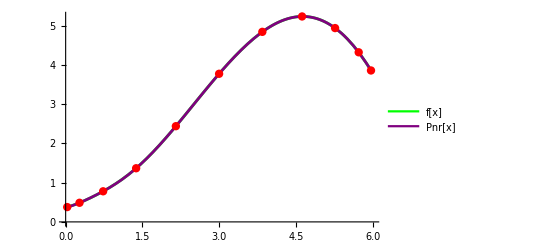

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Pnr[x]"}]]
```

```mathematica
в)
```

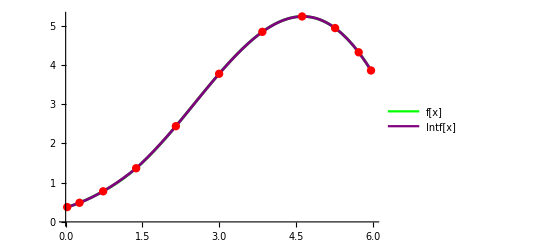

```mathematica
Intf=Interpolation[data];
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Purple},{"f[x]","Intf[x]"}]]
```

```mathematica
г)
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Pnr[2.4316]= ",Pnr/.x->2.4316];
Print[ "Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 2.8766

Pnr[2.4316]= 2.87698

Intf[2.4316]= 2.87618

```mathematica
д)
```

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},{x,0.1}]
```

{0.00239732,{x→0.119575}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},{x,3.4}]
```

{0.00139181,{x→3.4336}}

#### 3. Вывод : Увеличение количества узлов позволяет уменьшить погрешность интерполирования. Также неравномерное распределение узлов по отрезку позволяет уменьшить погрешность.

### Задание 4 .

```mathematica
б)
```

```mathematica
n=10; H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068

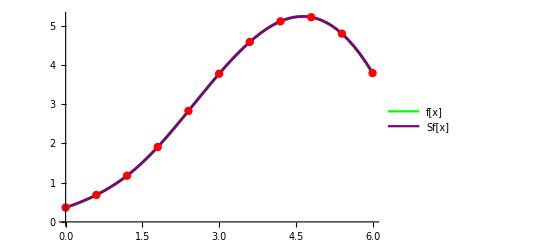

```mathematica
Sf=Interpolation[data,Method->"Spline"];
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.005]}];
func2=Plot[Sf[x],{x,dataX[[n+1]],B},PlotStyle->Purple];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Green, Purple},{"f[x]","Sf[x]"}]]
```

```mathematica
г)
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Sf[2.4316]= ",Sf[2.4316]];
```

f[2.4316]= 2.8766

Sf[2.4316]= 2.87665

### Задание 5 .

```mathematica
n=10; B=6; H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068

Q_1(x)=0.664812+0.815482 x

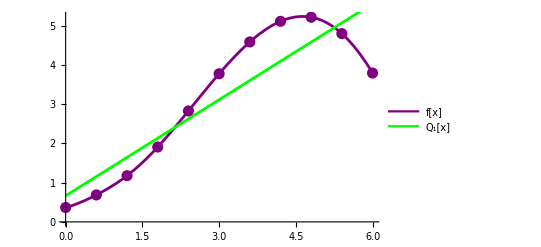

```mathematica
result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,1}]];
polinomialResult=0;
m=1;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 1]=polinomialResult;
Print["Q_1(x)=",Subscript[Q, 1]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Purple,Thickness[0.005]}];
func2=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Purple}];
Legended[Show[func1,func2,dots],LineLegend[{Purple,Green},{"f[x]","Q_1[x]"}]]
```

Q_2(x)=-0.342902+1.93516 x-0.186614 x^2

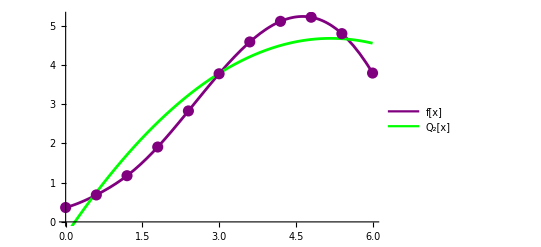

```mathematica
result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,2}]];
polinomialResult=0;
m=2;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 2]=polinomialResult;
Print["Q_2(x)=",Subscript[Q, 2]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Purple,Thickness[0.005]}];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Purple}];
Legended[Show[func1,func2,dots],LineLegend[{Purple,Green},{"f[x]","Q_2[x]"}]]
```

Q_3(x)=0.418786-0.081898 x+0.694969 x^2-0.0979536 x^3

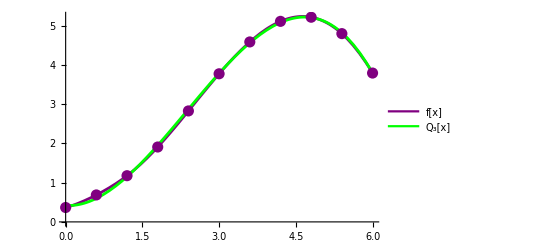

```mathematica
Subscript[Q, 3]=Fit[data,{1,x,x^2,x^3},x];
Print["Q_3(x)=",Subscript[Q, 3]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Purple,Thickness[0.005]}];
func2=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Purple}];
Legended[Show[func1,func2,dots],LineLegend[{Purple,Green},{"f[x]","Q_3[x]"}]]
```

Q_4(x)=0.397264+0.0426528 x+0.591177 x^2-0.0702757 x^3-0.0023065 x^4

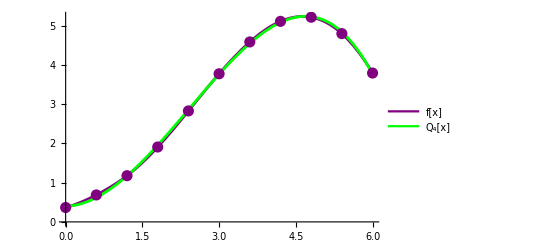

```mathematica
Subscript[Q, 4]=Fit[data,{1,x,x^2,x^3,x^4},x];
Print["Q_4(x)=",Subscript[Q, 4]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Purple,Thickness[0.005]}];
func2=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Purple}];
Legended[Show[func1,func2,dots],LineLegend[{Purple,Green},{"f[x]","Q_4[x]"}]]
```

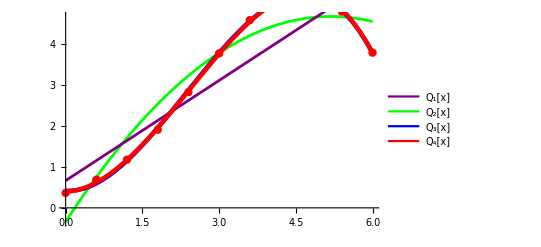

```mathematica
func1=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Purple];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Green];
func3=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->{Blue,Thickness[0.008]}];
func4=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->{Red,Thickness[0.008]}];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Red}];
Legended[Show[func2,func1,func3,func4,dots],LineLegend[{Purple,Green,Blue,Red},{"Q_1[x]","Q_2[x]","Q_3[x]","Q_4[x]"}]]
```